# fluid mediated impact - scales notes

B. Lecampion, J. Garcia-Suarez, J. Bilotto

## Scaling

Notation::
- R :: impactor radius of curvature
- zo :: initial tip distance   -> ϵ R ! 
- V ::   impactor velocity
- μp :: 12 μ    - // plate viscosity
- G :: solid shear modulus
- ρs :: solid density
- l  “dimple” length 
- P , T , L, H    characteristic pressure, time, dimple length,  solid deformation / gap scale etc.  
- Vf :: characteristic fluid velocity 
- po :: ambiance pressure

```mathematica
(*There are the dimensionless parameters that pop up in the equations*)
DimensionlessGroups={Gd-> L^2/(R H)(* dimple def. group -> from describing the contour of falling object *),
Ge-> (P L)/(G  H) (* quasi static elastic def -> solid boundary condition*),
Gk-> (P  T)/((M*ρs)^.5  H) (* highly dynamic localized compressive stress-> solid boundary condition*),
Gi-> (ρs  V L)/(T P)(* solid inertial/elastic group -> solid momentum *),
Gl-> H/(T V) (* group for fluid lubrication time-scale fall -> ratio time to fill the gap over a char. time *),
 Gm-> (μp L^2)/(P T H^2) (* lubrication group -> balance of viscous and inertial forces *),
Gc-> (P/po)  (* no need of γ power for scales -> for compressibility*)};
```

### Elastic - viscous scaling (small V)

```mathematica
(* this is elastic / low velocity scales*)
```

```mathematica
( # /.DimensionlessGroups)==1 & /@ {Gd, Gm,Ge,Gl}
```

{L^2/(H R)==1,(L^2 μp)/(H^2 P T)==1,(L P)/(G H)==1,H/(T V)==1}

```mathematica
Escales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Gd, Gm,Ge,Gl},{P,L, H,T }] [[1]]
```

{P→(G^(4/5) V^(1/5) μp^(1/5))/R^(1/5),L→(R^(4/5) V^(1/5) μp^(1/5))/G^(1/5),H→(R^(3/5) V^(2/5) μp^(2/5))/G^(2/5),T→(R^(3/5) μp^(2/5))/(G^(2/5) V^(3/5))}

the lubrication small parameter δ, valid for time and length scales where viscosity balances w/ elasticity

```mathematica
(H/L)/.Escales//PowerExpand
```

(V^(1/5) μp^(1/5))/(G^(1/5) R^(1/5))

```mathematica
L/R /.Escales//PowerExpand
```

(V^(1/5) μp^(1/5))/(G^(1/5) R^(1/5))

```mathematica
Egroups=DimensionlessGroups/.Escales//PowerExpand
```

{Gd→1,Ge→1,Gk→(G^(4/5) μp^(1/5))/(M^0.5 R^(1/5) V^(4/5) ρs^0.5),Gi→(R^(2/5) V^(8/5) ρs)/(G^(3/5) μp^(2/5)),Gl→1,Gm→1,Gc→(G^(4/5) V^(1/5) μp^(1/5))/(po R^(1/5))}

```mathematica
(* the Phi is Gi^(5/6) in the elastic scaling*)
```

```mathematica
Gi^(5/6)/.Egroups/. {G ->  ρs cs^2}//FullSimplify//PowerExpand
```

(R^(1/3) V^(4/3) ρs^(1/3))/(cs μp^(1/3))

Check the values (not so low, but low enough)

```mathematica
(R^(1/3) V^(4/3) ρs^(1/3))/(cs μp^(1/3))/.{R->10^-2,V->0.1,cs->7,ρs->1000,μp->12  10^-5.}
```

0.289629

Check the compressibility (compare local pressure to ambiance pressure)

```mathematica
Gc  /.Egroups//PowerExpand
```

(G^(4/5) V^(1/5) μp^(1/5))/(po R^(1/5))

```mathematica
(G^(4/5) V^(1/5) μp^(1/5))/(po R^(1/5))/.{G->  (1100 10^3)/(2 (1+0.5))  ,po-> 10^5.  ,R->10^-2,V->1.6,cs->7,ρs->1000,μp->12  10^-5.}
```

0.128256

```mathematica
Escales/.{G->  (250 10^3)/(2 (1+0.47))  ,po-> 10^5.  ,R->7.1*10^-3,V->0.065,ρs->1140,μp->12*1.81*10^-5.}
```

{P→2531.5,L→0.00021137,H→6.29256×10^-6,T→0.0000968086}

### Inertia - viscous scaling (larger V)

```mathematica
Iscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Gd, Gm,Gi,Gl},{P,L, H,T }] [[1]]
```

{P→(R^(1/3) V^(7/3) ρs^(4/3))/μp^(1/3),L→(R^(2/3) μp^(1/3))/(V^(1/3) ρs^(1/3)),H→(R^(1/3) μp^(2/3))/(V^(2/3) ρs^(2/3)),T→(R^(1/3) μp^(2/3))/(V^(5/3) ρs^(2/3))}

```mathematica
(* small parameter in the inertial regime *)
```

```mathematica
(H/L)/.Iscales//PowerExpand
```

μp^(1/3)/(R^(1/3) V^(1/3) ρs^(1/3))

```mathematica
(* link with stokes*)
StkRep={ Stk->  (ρs V R)/μp};
```

Check that H==R Stk^(-2/3)

```mathematica
(R Stk^(-2/3)/.StkRep //PowerExpand) == H/.Iscales
```

True

Check that L==R Stk^(-2/3)

```mathematica
(R Stk^(-1/3)/.StkRep //PowerExpand) == L/.Iscales
```

True

```mathematica
Igroups=DimensionlessGroups/.Iscales//PowerExpand
```

{Gd→1,Ge→(R^(2/3) V^(8/3) ρs^(5/3))/(G μp^(2/3)),Gk→(R^(1/3) V^(4/3) ρs^0.833333)/(M^0.5 μp^(1/3)),Gi→1,Gl→1,Gm→1,Gc→(R^(1/3) V^(7/3) ρs^(4/3))/(po μp^(1/3))}

Compressibility, indeed we see viscous/inertial pressures order ambiance

```mathematica
(R^(1/3) V^(7/3) ρs^(4/3))/(po μp^(1/3))/.{G->  (250 10^3)/(2 (1+0.5))  ,po-> 10^5.  ,R->10^-2,V->2.,ρs->1100,μp->12  10^-5.}
```

2.49958

```mathematica
((Gi/.Egroups)^(5/6)//PowerExpand) ==((Ge/.Igroups)^(1/2)//PowerExpand)
```

True

```mathematica
(Ge/.Igroups)^(1/2)//PowerExpand
```

(R^(1/3) V^(4/3) ρs^(5/6))/(√G μp^(1/3))

```mathematica
(P/.Iscales)/(P/.Escales)
```

(R^(8/15) V^(32/15) ρs^(4/3))/(G^(4/5) μp^(8/15))

```mathematica
(T/.Iscales)/(T/.Escales)
```

(G^(2/5) μp^(4/15))/(R^(4/15) V^(16/15) ρs^(2/3))

```mathematica
(H/.Iscales)/(H/.Escales)
```

(G^(2/5) μp^(4/15))/(R^(4/15) V^(16/15) ρs^(2/3))

```mathematica
Iscales/.{G->  (250 10^3)/(2 (1+0.47))  ,po-> 10^5.  ,R->7.1*10^-3,V->1.01,ρs->1140,μp->12*1.81*10^-5.} (*Intermediate regime values*)
```

{P→38972.3,L→0.000211861,H→6.32182×10^-6,T→6.25922×10^-6}

```mathematica
Iscales/.{G->  (250 10^3)/(2 (1+0.47))  ,po-> 10^5.  ,R->7.1*10^-3,V->2.05,ρs->1140,μp->12*1.81*10^-5.} (*Inertial regime values plot*)
```

{P→203282.,L→0.00016733,H→3.94355×10^-6,T→1.92368×10^-6}

### Viscous - compressibility scaling (even larger V)

```mathematica
(* - viscous and compressibility (compressiblity takes over inertia) *)
```

```mathematica
VCscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Gc,Gm, Gd,Gl},{P,L, H,T }][[-1]]//Simplify
```

{P→po,L→(R^(3/4) V^(1/4) μp^(1/4))/po^(1/4),H→(√R √V √μp)/(√po),T→(√R √μp)/(√po √V)}

```mathematica
H/L/.VCscales
```

(V^(1/4) μp^(1/4))/(po^(1/4) R^(1/4))

```mathematica
VCgroups=DimensionlessGroups/.VCscales//PowerExpand
```

{Gd→1,Ge→(po^(5/4) R^(1/4))/(G V^(1/4) μp^(1/4)),Gk→po/(M^0.5 V ρs^0.5),Gi→(R^(1/4) V^(7/4) ρs)/(po^(3/4) μp^(1/4)),Gl→1,Gm→1,Gc→1}

```mathematica
(* note that in the case of fluid droplet there is no elasticity *)
(* the ϵ of Mandre is thus linked to Gi  !! *)
```

```mathematica
Gi^(-4/3)/.VCgroups //PowerExpand
```

(po μp^(1/3))/(R^(1/3) V^(7/3) ρs^(4/3))

```mathematica
(Gc/.Igroups)^-1//PowerExpand  (* Gc Inertia = to mandre ϵ^-1*)
```

(po μp^(1/3))/(R^(1/3) V^(7/3) ρs^(4/3))

```mathematica
(Gc/.Egroups)^-1//PowerExpand  (* Gc elastic, another ϵ^-1 for the case compressibility is relevant in the elastic regime*)
```

(po R^(1/5))/(G^(4/5) V^(1/5) μp^(1/5))

```mathematica
(po R^(1/5))/(G^(4/5) V^(1/5) μp^(1/5))/.{G->  (1100 10^3)/(2 (1+0.5))  ,po-> 10^5.  ,R->7.1*10^-3,V->10,ρs->1140,μp->12*1.81*10^-5.}
```

4.4819

```mathematica
(Kb R^(1/5))/(G^(4/5) V^(1/5) μp^(1/5))/.{G->  (1100 10^3)/(2 (1+0.5))  ,Kb-> (675*10^3)/(3(1-2*.1))  ,R->7.1*10^-3,V->10,ρs->1140,μp->12*1.81*10^-5.}
```

12.6054

### Elastic- compressibility scaling (NEW)

```mathematica
Kscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Gk,Gm, Gd,Gl},{P,L, H,T }][[-1]]//Simplify//PowerExpand
```

{P→√M V √ρs,L→(R^(3/4) μp^(1/4))/(M^(1/8) ρs^(1/8)),H→(√R √μp)/(M^(1/4) ρs^(1/4)),T→(√R √μp)/(M^(1/4) V ρs^(1/4))}

```mathematica
Kscales = Simplify[Kscales, Assumptions->{K>0, G>0}]
```

{P→√M V √ρs,L→(R^(3/4) μp^(1/4))/(M^(1/8) ρs^(1/8)),H→(√R √μp)/(M^(1/4) ρs^(1/4)),T→(√R √μp)/(M^(1/4) V ρs^(1/4))}

```mathematica
H/L/.Kscales//PowerExpand
```

μp^(1/4)/(M^(1/8) R^(1/4) ρs^(1/8))

```mathematica
Kgroups=DimensionlessGroups/.Kscales//PowerExpand
```

{Gd→1,Ge→(M^(5/8) R^(1/4) V ρs^(5/8))/(G μp^(1/4)),Gk→1.,Gi→(R^(1/4) V ρs^(5/8))/(M^(3/8) μp^(1/4)),Gl→1,Gm→1,Gc→(√M V √ρs)/po}

We recover the transition parameter as V/(c_p*St) (I don’t know why it wrote 5/6 as 0.833 in the exponent for density)

```mathematica
Gk/.Igroups //PowerExpand (*Transition from inertial to compressible solid*)
```

(R^(1/3) V^(4/3) ρs^0.833333)/(M^0.5 μp^(1/3))

```mathematica
(Gi/.Kgroups) == ((Gk /.Igroups)^(3/4)//PowerExpand)
```

True

## Intermediate Regime (balance elastic-inertial)

```mathematica
TRscales=Solve[ ( # /.DimensionlessGroups)==1 & /@ {Ge,Gm, Gl,Gi},{P,L, H,T }][[-1]]//Simplify
```

{P→√G V √ρs,L→(G μp)/(V^3 ρs^2),H→(√G μp)/(V^2 ρs^(3/2)),T→(√G μp)/(V^3 ρs^(3/2))}

```mathematica
H/L/.TRscales
```

(V √ρs)/(√G)

```mathematica
TRgroups=DimensionlessGroups/.TRscales//PowerExpand
```

{Gd→(G^(3/2) μp)/(R V^4 ρs^(5/2)),Ge→1,Gk→(1. √G)/M^0.5,Gi→1,Gl→1,Gm→1,Gc→(√G V √ρs)/po}

### cross - over

```mathematica
(* the Phi is Gi^(5/6) in the elastic scaling*)
```

in terms of velocities

```mathematica
repϕ={ϕ->Gi^(5/6)/.Egroups /.{G ->  ρs cs^2}//PowerExpand}
```

{ϕ→(R^(1/3) V^(4/3) ρs^(1/3))/(cs μp^(1/3))}

in terms of G

```mathematica
repϕG={ϕ->Gi^(5/6)/.Egroups //PowerExpand}
```

{ϕ→(R^(1/3) V^(4/3) ρs^(5/6))/(√G μp^(1/3))}

Compare the ratio of timescales in both the inertial and elastic regime

```mathematica
(T/.Iscales)/(T/.Escales)//PowerExpand
```

(G^(2/5) μp^(4/15))/(R^(4/15) V^(16/15) ρs^(2/3))

Same thing for the gap sizes:

```mathematica
{Gi/.Egroups,Ge/.Igroups}
```

{(R^(2/5) V^(8/5) ρs)/(G^(3/5) μp^(2/5)),(R^(2/3) V^(8/3) ρs^(5/3))/(G μp^(2/3))}

```mathematica
(T/.Iscales)/(T/.Escales)//PowerExpand
```

(G^(2/5) μp^(4/15))/(R^(4/15) V^(16/15) ρs^(2/3))

```mathematica
(L/.Escales) ==  (L/.Iscales)  (ϕ /.repϕG)^(2/5)//PowerExpand
```

True

```mathematica
(H/.Escales) ==  (H/.Iscales)  (ϕ /.repϕG)^(4/5)//PowerExpand
```

True

## Order of magnitude and cross over

```mathematica
(* I think putting the 12 in the scales is warranted - see Carlo's energy budget for HF *)
```

```mathematica
parameterSOFT={G->  (250 10^3)/(2 (1+0.5))  ,R-> 7.1 10^-3,ρs-> 1140 ,μp->12*1.81* 10^-5.,po-> 10^5. , K -> (250*10^3)/(2(1-0.47)) , ν->0.47}
```

{G→83333.3,R→0.0071,ρs→1140,μp→0.0002172,po→100000.,K→235849.,ν→0.47}

```mathematica
parametersHard={G->  (1100 10^3)/(2 (1+0.5))  ,R-> 7.1 10^-3,ρs-> 1140 ,μp->12*1.81 10^-5.,po-> 10^5., K -> (1100*10^3)/(2(1-0.47)) ,  ν->0.47 }
```

{G→366667.,R→0.0071,ρs→1140,μp→0.0002172,po→100000.,K→1.03774×10^6,ν→0.47}

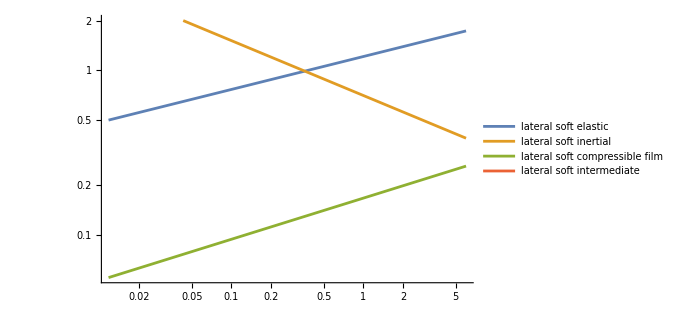

```mathematica
LogLogPlot[{ 3.3*10^3 L/.Escales /.parameterSOFT,
3.3*10^3 L/.Iscales /.parameterSOFT,
10^3 L/.VCscales /.parameterSOFT,
 10^3 L/.Kscales /.parameterSOFT(*10^3 L/.EIscales /.parameterSOFT*)},
{V,0.,6.},PlotRange->{0.,2},ImageSize->500,
PlotLegends->{"lateral soft elastic","lateral soft inertial", "lateral soft compressible film","lateral soft intermediate" }]
```

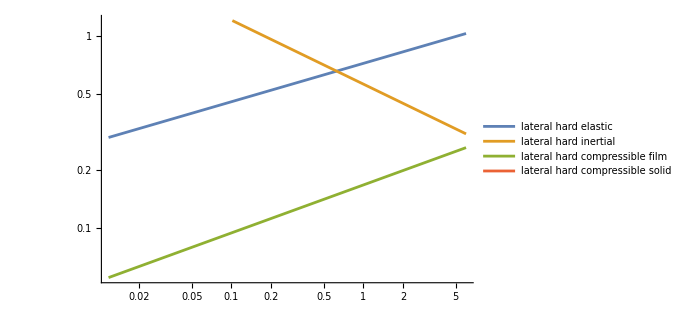

```mathematica
LogLogPlot[{ 10^3 3.8/3^(1/3)*L/.Escales /.parametersHard,
10^3 3.8/3^(1/3)*L/.Iscales /.parametersHard,
10^3 L/.VCscales /.parametersHard,
10^3 L/.Kscales /.parametersHard},{V,0.,6.},PlotRange->{0.,1.2},ImageSize->500,
PlotLegends->{"lateral hard elastic","lateral hard inertial", "lateral hard compressible film", "lateral hard compressible solid"}]
```

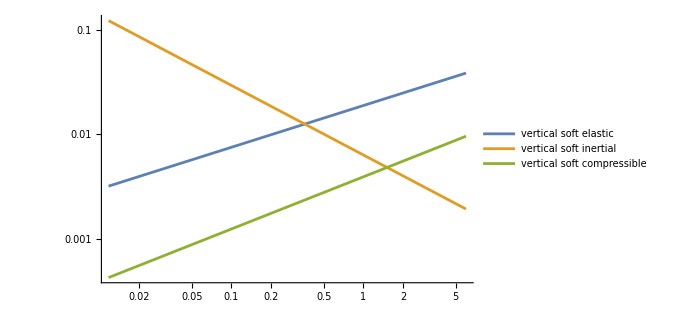

```mathematica
LogLogPlot[{ 10^3 H/.Escales /.parameterSOFT,
10^3 H/.Iscales /.parameterSOFT,
10^3 H/.VCscales /.parameterSOFT(*,10^3 H/.EIscales /.parameterSOFT*)},
{V,0.,6.},PlotRange->Automatic,ImageSize->500,
PlotLegends->{"vertical soft elastic","vertical soft inertial","vertical soft compressible"}]
```

Velocity ratio soft impactor:

```mathematica
((L/T)/√(G/ρs) /.Iscales//PowerExpand)/.parameterSOFT
```

3.90671 V^(4/3)

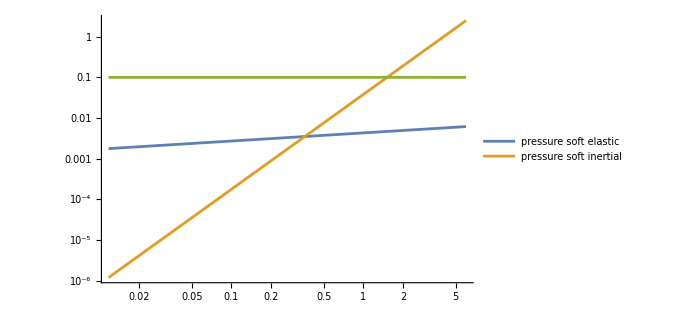

```mathematica
LogLogPlot[{  10^-6 P/.Escales /.parameterSOFT,
10^-6 P/.Iscales /.parameterSOFT,
10^-6 P/.VCscales /.parameterSOFT},{V,0.,6.},PlotRange->Automatic,ImageSize->500,
PlotLegends->{"pressure soft elastic","pressure soft inertial"}]
```

```mathematica
(* when compressibility will start to play a role !!  when Gc in the inertial scaling becomes order 1 *)
```

```mathematica
Solve[(Gc/.Igroups/.parameterSOFT)==1. ,V]
```

{{V→1.51256}}

```mathematica
(* when compressibility will start to play a role !!  when Gc in the elastic scaling becomes order 1, this never happens, but it could for very hard solids*)
```

```mathematica
Solve[(Gc/.Egroups/.parameterSOFT)==1. ,V]
```

{{V→6.77834×10^6}}

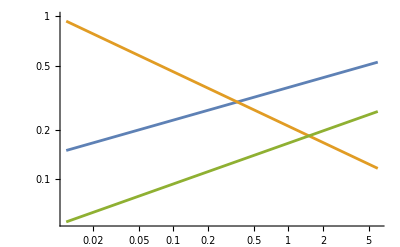

```mathematica
LogLogPlot[{ 10^3 L/.Escales /.parameterSOFT,10^3 L/.Iscales /.parameterSOFT,10^3 L/.VCscales /.parameterSOFT},{V,0.,6.}]
```

```mathematica
(*Plot[{ 10^3 L/.Escales /.parametersHard,10^3 L/.Iscales /.parametersHard,10^3 L/.VCscales /.parametersHard},{V,0.,6.},PlotRange->{0.,1.2},ImageSize->500]*P)
```